```mathematica
mat = {{"P","D"},{"S","P"},{"D","S"}}
```

{{P,D},{S,P},{D,S}}

```mathematica
base={RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.6705882352941176, 0.8509803921568627, 1],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451]}
```

{RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.6705882352941176, 0.8509803921568627, 1],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451]}

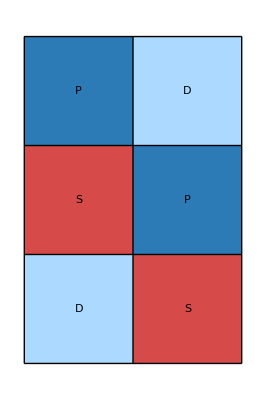

```mathematica
ArrayPlot[mat,ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[mat],{2}]},Mesh->True,MeshStyle->Black]
```

Individual nodes of the interaction graph:

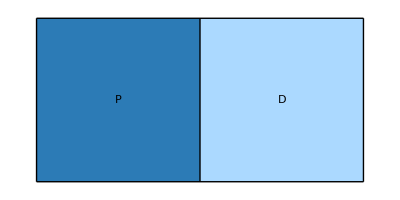

```mathematica
ArrayPlot[{mat[[1]]},ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[{mat[[1]]}],{2}]},Mesh->True,MeshStyle->Black]
```

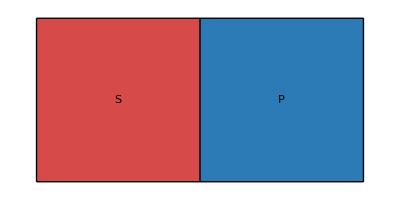

```mathematica
ArrayPlot[{mat[[2]]},ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[{mat[[2]]}],{2}]},Mesh->True,MeshStyle->Black]
```

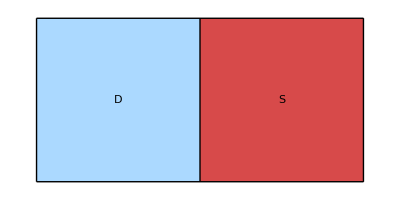

```mathematica
ArrayPlot[{mat[[3]]},ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[{mat[[3]]}],{2}]},Mesh->True,MeshStyle->Black]
```